## Enlargement

```mathematica
enlargePolygon[vertices_,scaleFactor_,center_]:=Module[{originalPolygon,enlargedPolygon,plotTitle},(*Create the original polygon from vertices*)originalPolygon=ConvexHullMesh[vertices];
(*Create the enlarged polygon using geometric transformation*)enlargedPolygon=GeometricTransformation[originalPolygon,ScalingTransform[{scaleFactor,scaleFactor},center]];
(*Create plot title*)plotTitle="Polygon Enlargement with Scale Factor = "<>ToString[scaleFactor]<>" from Center "<>ToString[center];
(*Determine an appropriate plot range based on original and enlarged vertices*)allPoints=Join[vertices,Table[center+scaleFactor*(vertices[[i]]-center),{i,1,Length[vertices]}],{center}];
xMin=Min[allPoints[[All,1]]]-1;
xMax=Max[allPoints[[All,1]]]+1;
yMin=Min[allPoints[[All,2]]]-1;
yMax=Max[allPoints[[All,2]]]+1;
(*Create and return the plot*)Graphics[{(*Enlarged polygon-slightly transparent*){LightPink,Opacity[0.6],enlargedPolygon},(*Original polygon*){LightOrange,Opacity[1],originalPolygon},(*Center point*){Red,PointSize[0.02],Point[center]},Text["Center: "<>ToString[center],center,{-1,-1}],(*Original vertices*){Green,PointSize[0.015],Point[vertices]},Table[Text["v"<>ToString[i]<>": "<>ToString[vertices[[i]]],vertices[[i]],{0,1}],{i,1,Length[vertices]}],(*Enlarged vertices*){Orange,PointSize[0.015],Point[Table[center+scaleFactor*(vertices[[i]]-center),{i,1,Length[vertices]}]]},(*Connection lines between original and enlarged vertices*){Gray,Dashed,Table[Line[{vertices[[i]],center+scaleFactor*(vertices[[i]]-center)}],{i,1,Length[vertices]}]}},Frame->True,Axes->True,AxesLabel->{"x","y"},AxesStyle->Thick,GridLines->{Range[-100,100,1],Range[-100,100,1]},PlotRange->{{xMin,xMax},{yMin,yMax}},PlotLabel->plotTitle,ImageSize->600]]
(*Deploy a simple form interface*)
CloudDeploy[FormFunction[{"vertices"->"String","center"->"String","scaleFactor"->"Number"},Module[{vertexList,centerPoint},(*Parse the input string of vertices*)vertexList=ToExpression[#vertices];
(*Parse the center point*)centerPoint=ToExpression[#center];
(*Run the function with user inputs*)enlargePolygon[vertexList,#scaleFactor,centerPoint]]&,"PNG"],"SimpleEnlargementTool",Permissions->"Public"]
```

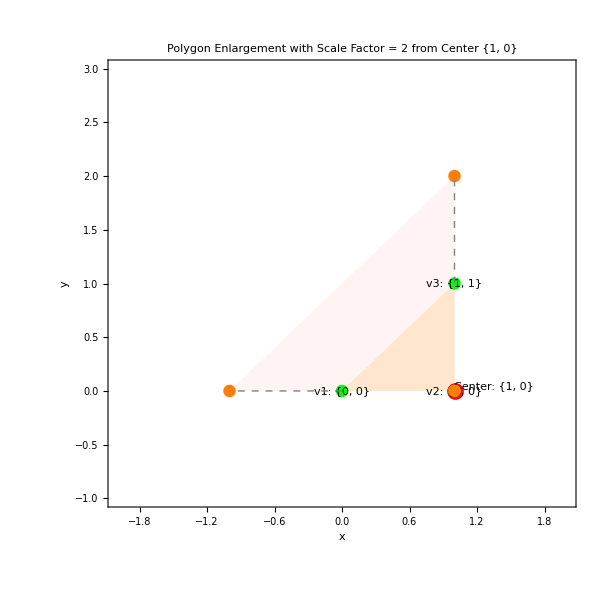

```mathematica
enlargePolygon[{{0,0},{1,0},{1,1}},2,{1,0}]
```